## Get helper functions

```mathematica
NotebookEvaluate[FileNameJoin[{ParentDirectory[ParentDirectory[NotebookDirectory[]]],"UTILITY_readBeamFiles.nb"}]]
```

```mathematica
fileNums = Range[0,20]
fileNames = NotebookDirectory[]<>ToString[#]<>".h5"&/@fileNums
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

{/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/0.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/1.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/2.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/3.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/4.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/5.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/6.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/7.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/8.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/9.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/10.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/11.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/12.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/13.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/14.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/15.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/16.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/17.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/18.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/19.h5,/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/20.h5}

## Process single

```mathematica
data = readBeamFile[fileNames[[1]]];
```

```mathematica
scaledData = {
10^6#x,
10^6#px/#pz,
10^6#y,
10^6#py/#pz,
10^6#z,
10^-9#pz
}&/@data;
```

```mathematica
iqrRangeScale = 4;
```

```mathematica
dataRanges = {
Median[#]-iqrRangeScale*InterquartileRange[#],
Median[#]+iqrRangeScale*InterquartileRange[#]
}&/@Transpose[scaledData]
```

{{-143.057,164.098},{-875.275,847.696},{-174.141,135.524},{-250.505,97.2431},{-177.603,195.338},{9.11026,10.5327}}

```mathematica
Length[scaledData]
clippedData =Select[
scaledData,
RegionMember[
rangeCuboid = Cuboid[dataRanges[[All,1]],dataRanges[[All,2]]],
#
]&
];
Length[clippedData]
```

99978

98978

```mathematica
imageSize=800;
rasterSize = 800;
```

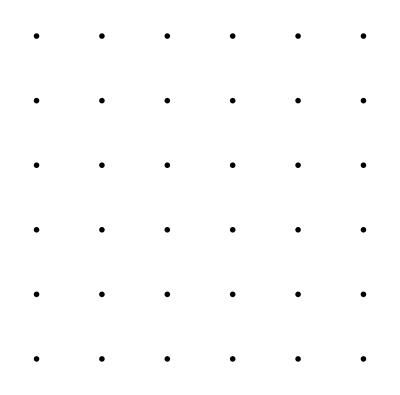

```mathematica
GraphicsGrid[
ParallelTable[
If[i!=j,
Rasterize[
densityHistogramMod[
clippedData[[All,{i,j}]],
{50,50},
ImageSize->imageSize,
PlotRange->{dataRanges[[i]],dataRanges[[j]]},
LabelStyle->20
],RasterSize->rasterSize],
Rasterize[
Histogram[
clippedData[[All,i]],
{(dataRanges[[i,2]]-dataRanges[[i,1]])/50},
ImageSize->imageSize,
PlotRange->{dataRanges[[i]],Automatic},
LabelStyle->20
],RasterSize->rasterSize]
],
{i,1,6},
{j,1,6}
]]
```

## Automate (hold plot ranges constant)

```mathematica
Dynamic[fileName]
imgArr = Table[
data = readBeamFile[fileName];

scaledData = {
10^6#x,
10^6#px/#pz,
10^6#y,
10^6#py/#pz,
10^6#z,
10^-9#pz
}&/@data;

clippedData =Select[
scaledData,
RegionMember[
rangeCuboid = Cuboid[dataRanges[[All,1]],dataRanges[[All,2]]],
#
]&
];

GraphicsGrid[
ParallelTable[
If[i!=j,
Rasterize[
densityHistogramMod[
clippedData[[All,{i,j}]],
{50,50},
ImageSize->imageSize,
PlotRange->{dataRanges[[i]],dataRanges[[j]]},
LabelStyle->20
],RasterSize->rasterSize],
Rasterize[
Histogram[
clippedData[[All,i]],
{(dataRanges[[i,2]]-dataRanges[[i,1]])/50},
ImageSize->imageSize,
PlotRange->{dataRanges[[i]],Automatic},
LabelStyle->20
],RasterSize->rasterSize],
ImageSize->2400
],
{i,1,6},
{j,1,6}
]],

{fileName,fileNames}
];
```

```mathematica
Export[NotebookDirectory[]<>"anim.gif",imgArr,ImageSize->2400]
```

/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/2024-12-16_sextupoleStudy/Animation - random errors/anim.gif